```mathematica
ClearAll["Global`*"];
```

Parameter assumptions

```mathematica
$Assumptions={ω∈Reals,χ∈Reals,κ∈Reals&&κ≥0,t∈Reals&&t≥0,s∈Reals&&s≥0,Ω∈Reals,x[t]∈Reals,p[t]∈Reals,x'[t]∈Reals,p'[t]∈Reals,ϵ1[t]∈Reals,ϵ2[t]∈Reals,α∈Reals,β∈Reals,σ∈Reals};
```

Langevin Equation

```mathematica
Le[t_,ω_,κ_,σ_]=D[a[t],t]+I*ω*σ*a[t]+κ/2*a[t]+Ω[t];
TraditionalForm[Le[t,ω,κ,σ]]
```

a'(t)+1/2 κ a(t)+ⅈ σ ω a(t)+Ω(t)

Separate in Real and imaginary part

```mathematica
LeRI[t_,ω_,κ_,σ_]=Le[t,ω,κ,σ]/.{a[t]->x[t]+I*p[t],a'[t]->x'[t]+I*p'[t],Ω[t]->ϵ1[t]+I*ϵ2[t]};
TraditionalForm[LeRI[t,ω,κ,σ]]
```

ⅈ p'(t)+1/2 κ (x(t)+ⅈ p(t))+ⅈ σ ω (x(t)+ⅈ p(t))+x'(t)+ϵ1(t)+ⅈ ϵ2(t)

Write the differential equation as a linear system

```mathematica
X[t_]={x[t],p[t]};
```

```mathematica
u[t_]={ϵ1[t],ϵ2[t]};
```

```mathematica
A=-{Grad[FullSimplify[Re[LeRI[t,ω,κ,σ]]],X[t]],Grad[FullSimplify[Im[LeRI[t,ω,κ,σ]]],X[t]]};
TraditionalForm[A]
```

(-κ/2 | σ ω
-σ ω | -κ/2)

```mathematica
B=-{Grad[FullSimplify[Re[LeRI[t,ω,κ,σ]]],u[t]],Grad[FullSimplify[Im[LeRI[t,ω,κ,σ]]],u[t]]};
TraditionalForm[B]
```

(-1 | 0
0 | -1)

Optimal control Pulse

```mathematica
Xf={α,β};
X0={0,0};
```

```mathematica
μ1=FullSimplify[Inverse[Integrate[MatrixExp[A*(s-t)].B.Transpose[B].Transpose[MatrixExp[A*(s-t)]],{t,0,s}]]];
TraditionalForm[μ1]
```

(κ (1/(ⅇ^(κ s)-1)+1) | 0
0 | κ (1/(ⅇ^(κ s)-1)+1))

```mathematica
μ2=(Xf-MatrixExp[A*s].X0);
```

```mathematica
μ=FullSimplify[μ1.μ2];
```

```mathematica
uopt[t_,s_,ω_,κ_,σ_,α_,β_]=FullSimplify[2*Transpose[B].Transpose[MatrixExp[A*(s-t)]].μ];
TraditionalForm[uopt[t,s,ω,κ,σ,α,β]]
```

{-(2 κ ⅇ^(1/2 κ (s+t)) (α cos(σ ω (s-t))-β sin(σ ω (s-t))))/(ⅇ^(κ s)-1),-(2 κ ⅇ^(1/2 κ (s+t)) (α sin(σ ω (s-t))+β cos(σ ω (s-t))))/(ⅇ^(κ s)-1)}

```mathematica
u1=FullSimplify[uopt[t,tf,χ,κ,1,α,β][[1]]+I*uopt[t,tf,χ,κ,1,α,β][[2]]]
u2=FullSimplify[uopt[t,tf,χ,κ,1,α,β][[1]]-I*uopt[t,tf,χ,κ,1,α,β][[2]]]
```

-(2 ⅇ^(1/2 (t+tf) κ+ⅈ (-t+tf) χ) (α+ⅈ β) κ)/(-1+ⅇ^(tf κ))

-(2 ⅇ^(1/2 (t+tf) κ+ⅈ (t-tf) χ) (α-ⅈ β) κ)/(-1+ⅇ^(tf κ))

```mathematica
Leopt[t_,s_,χ_,κ_,σ_,α_,β_]=Le[t,χ,κ,σ]/.{Ω[t]->uopt[t,s,χ,κ,σ,α,β][[1]]+I*uopt[t,s,χ,κ,σ,α,β][[2]]};
```

```mathematica
Solopt[t_,s_,χ_,κ_,σ_,α_,β_]=FullSimplify[DSolve[{Leopt[t,s,χ,κ,σ,α,β]==0,a[0]==0},a[t],t]]
```

{{a[t]→(2 ⅇ^(1/2 (s-t) (κ+2 ⅈ σ χ)) (-1+ⅇ^(t κ)) (α+ⅈ β))/(-1+ⅇ^(s κ))}}

```mathematica
a1=(2 ⅇ^(1/2 (-t+tf) (κ1+2 ⅈ χ1)) (-1+ⅇ^(t κ1)) (α+ⅈ β))/(-1+ⅇ^(tf κ1));
a2=(2 ⅇ^(1/2 (-t+tf) (κ1-2 ⅈ χ1)) (-1+ⅇ^(t κ1)) (α-ⅈ β))/(-1+ⅇ^(tf κ1));
```

```mathematica
af=10*(-κ/2+I*χ*σ)/Abs[-κ/2+I*χ*σ]/.{χ->0.25,κ->2*π*0.01,σ->1}
```

-1.24683+9.92197 ⅈ

```mathematica
Calopt2a=N[Solve[{FullSimplify[Re[Solopt[10,10,2π*0.3,2*π*0.01,1,α,β][[1,1,2]]]]==10*Re[af],FullSimplify[Im[Solopt[10,10,2π*0.3,2*π*0.01,1,α,β][[1,1,2]]]]==10*Im[af]},{α,β},Reals]]
Calopt2b=N[Solve[{FullSimplify[Re[Solopt[10,10,2π*0.3,2*π*0.01,-1,α,β][[1,1,2]]]]==10*Re[af],FullSimplify[Im[Solopt[10,10,2π*0.3,2*π*0.01,-1,α,β][[1,1,2]]]]==10*Im[af]},{α,β},Reals]]
```

{{α→-6.23416,β→49.6098}}

{{α→-6.23416,β→49.6098}}

```mathematica
χ=2π*0.3;
κ=2π*0.01;
n=10;
ϵtem=10;
```

```mathematica
lesol=Le[t,2π*0.3,κ,1]==0/.Ω[t]->uopt[t,10,2π*0.3,2π*0.01,1,5,0][[1]]+I*uopt[t,10,2π*0.3,2π*0.01,1,5,0][[2]];
```

```mathematica
sol1[t_]=DSolve[{lesol,a[0]==0},{a[t]},{t}][[1,1,2]];
ds[t_]=D[sol1[t],t];
```

```mathematica
geo0[t_]:=ArcCos[Abs[Exp[-1/2*(Abs[sol1[t]]^2)]]]/NIntegrate[Abs[ds[tt]],{tt,0,t}];
mt0[t_]:=Sin[ArcCos[Exp[-Abs[sol1[t]]^2/2]]]^2/(Sqrt[2]*NIntegrate[Abs[ds[tt]],{tt,0,t}]);
ml0[t_]:=Sin[ArcCos[Exp[-Abs[sol1[t]]^2/2]]]^2/(2*NIntegrate[Abs[ds[tt]],{tt,0,t}]);
```

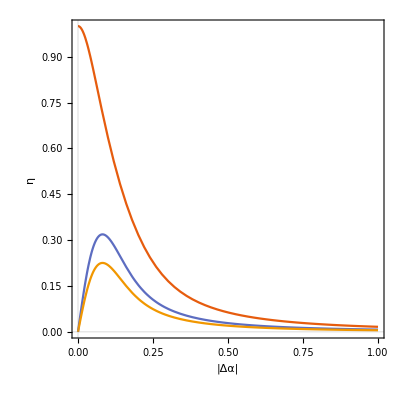

```mathematica
figen=ParametricPlot[{{Abs[sol1[t]]/10,geo0[t]},{Abs[sol1[t]]/10,mt0[t]},{Abs[sol1[t]]/10,ml0[t]}},{t,10^-5,10},PlotRange->{{0,1},{0,1}},PlotTheme->"Scientific",FrameLabel->{"|Δα|","η"},LabelStyle->Directive[Black,16,FontFamily->"Times"](*,PlotStyle->Blue*)]
```

```mathematica
etaen=Table[{Abs[sol1[t*10/100]]/10,geo0[t*10/100],mt0[t*10/100],ml0[t*10/100]},{t,1,100}];
Export["C:\\Users\\Mo Zhou\\python file\\paint\\新建文件夹\\etaen.csv",etaen];
```

```mathematica
sindriving[t_,e_,tf_]=e Sin[π/2*t/tf]^2;
cddriving[t_,χ_,κ_,σ_,e_,tf_]=sindriving[t,e,tf]-I*D[sindriving[t,e,tf],t]/(χ*σ-I*κ/2);
```

```mathematica
Lecd[t_,χ_,κ_,σ_,e_,tf_,α_,β_]=Le[t,χ,κ,σ]/.{Ω[t]->cddriving[t,χ,κ,σ,e,tf]};
Solcd[t_,χ_,κ_,σ_,e_,tf_,α_,β_]=FullSimplify[DSolve[{Lecd[t,χ,κ,σ,e,tf,α,β]==0,a[0]==0},a[t],t]]
```

{{a[t]→(e (0.00442097+(0.+0.265258 ⅈ) σ+(-0.00442097-(0.+0.265258 ⅈ) σ) Cos[(3.14159 t)/tf]))/(-0.000277778+σ ((0.-0.0333333 ⅈ)+1. σ))}}

```mathematica
Ledi[t_,χ_,κ_,σ_,e_,tf_,α_,β_]=Le[t,χ,κ,σ]/.{Ω[t]->sindriving[t,e,tf]};
Soldi[t_,χ_,κ_,σ_,e_,tf_,α_,β_]=FullSimplify[DSolve[{Ledi[t,χ,κ,σ,e,tf,α,β]==0,a[0]==0},a[t],t]];
```

Solve amplitude to get final state

```mathematica
ampsol[t_,χ_,κ_,σ_,tf_,α_,β_]=Solve[Solcd[t,χ,κ,σ,e,tf,α,β][[1,1,2]]==α+I*β,e][[1,1,2]]
```

((1. α+(0.+1. ⅈ) β) (-0.000277778+σ ((0.-0.0333333 ⅈ)+1. σ)))/(0.00442097+(0.+0.265258 ⅈ) σ+(-0.00442097-(0.+0.265258 ⅈ) σ) Cos[(3.14159 t)/tf])

Set the final state α, β

```mathematica
Calopt1a={{α->Re[af],β->Im[af]}}
e1=ampsol[10,2.5,2π*0.01,1,10,α,β]/.Calopt1a[[1]]
```

{{α→-1.24683,β→9.92197}}

18.7416+2.03851 ⅈ

```mathematica
cd1[t_]=Solcd[t,χ,κ,1,e1,10,Re[af],Im[af]][[1,1,2]];
cd2[t_]=D[cd1[t],t];
geo2[t_]=ArcCos[Abs[Exp[-1/2*(Abs[cd1[t]]^2)(*+sol1[t]*)]]]/Integrate[Abs[cd2[tt]],{tt,0,t}];
mt2[t_]:=Sin[ArcCos[Exp[-Abs[cd1[t]]^2/2]]]^2/(Sqrt[2]*NIntegrate[Abs[cd2[tt]],{tt,0,t}]);
ml2[t_]:=Sin[ArcCos[Exp[-Abs[cd1[t]]^2/2]]]^2/(2*NIntegrate[Abs[cd2[tt]],{tt,0,t}]);
```

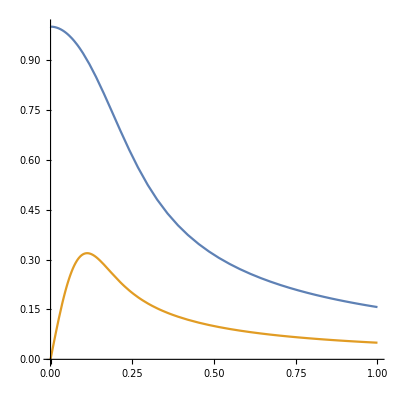

```mathematica
figcd=ParametricPlot[{{Abs[cd1[t]]/10,geo2[t]}(*,{Abs[cd1[t]]/10,mt2[t]}*),{Abs[cd1[t]]/10,ml2[t]}},{t,10^-5,9.999},PlotRange->{0,1}]
```

```mathematica
etacd=Table[{Abs[cd1[t*9.99/100]]/10,geo2[t*9.99/100],mt2[t*9.99/100],ml2[t*9.99/100]},{t,1,100}];
Export["C:\\Users\\Mo Zhou\\python file\\paint\\新建文件夹\\etacd.csv",etacd];
```

```mathematica
cdterm=cddriving[t,χ,κ,1,e1,10]-sindriving[t,e1,10];
```

```mathematica
ad1[t_]=Soldi[t,χ,κ,1,e1,10,Re[af],Im[af]][[1,1,2]];
ad2[t_]=D[ad1[t],t];
```

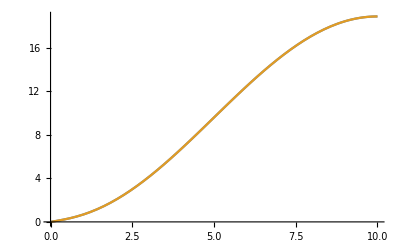

```mathematica
sindriving[t_,e_,tf_]=e Sin[π/2*t/tf]^2;
cddriving[t_,χ_,κ_,σ_,e_,tf_]=sindriving[t,e,tf]-I*D[sindriving[t,e,tf],t]/(χ*σ-I*κ/2);
cdterm=cddriving[t,χ,κ,1,e1,10]-sindriving[t,e1,10];
Plot[{Abs[cdterm+sindriving[t,e1,10]],Abs[cddriving[t,χ,κ,1,e1,10]]},{t,0,10}]
```

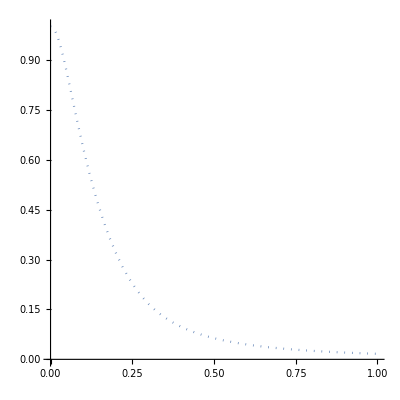

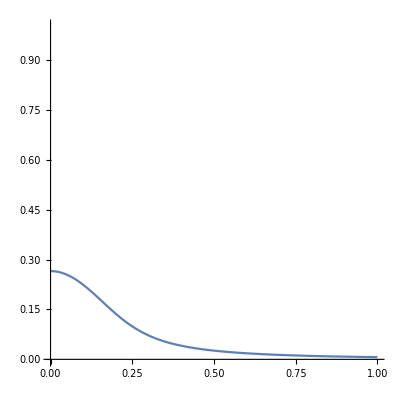

```mathematica
mean1[t_]=-2Im[D[sol1[t],t]*Conjugate[sol1[t]]];
var1[t_]=Abs[D[sol1[t],t]];
den1[t_]=D[enbar[t],t];
Plot[ArcCos[Exp[-Abs[enbar[t]]^2/2]]/NIntegrate[var1[tt],{tt,0,t}],{t,0,10},PlotRange->{0,1}];
enfig1=ParametricPlot[{Abs[sol1[t]]/Abs[sol1[10]],ArcCos[Exp[-Abs[sol1[t]]^2/2]]/NIntegrate[var1[tt],{tt,0,t}]},{t,10^-4,10},PlotRange->{{0,1},{0,1}},PlotStyle->Dotted]
enfig2=ParametricPlot[{Abs[sol1[t]]/Abs[sol1[10]],ArcCos[Exp[-Abs[sol1[t]]^2/2]]^2/mean1[t]},{t,10^-4,10},PlotRange->{{0,1},{0,1}}]
```

```mathematica
enmean=Table[{Abs[sol1[t*10/1001]],ArcCos[Exp[-Abs[sol1[t*10/1001]]^2/2]]/NIntegrate[mean1[tt],{tt,0,t*10/1001}]},{t,1,1001}];
envar=Table[{Abs[sol1[t*10/1001]],ArcCos[Exp[-Abs[sol1[t*10/1001]]^2/2]]/NIntegrate[var1[tt],{tt,0,t*10/1001}]},{t,1,1001}];
Export["C:\\Users\\Mo Zhou\\python file\\paint\\enmean.csv",enmean];
Export["C:\\Users\\Mo Zhou\\python file\\paint\\envar.csv",envar];
```

```mathematica
Plot[{Im[sol1[t]],Im[t1[t]]},{t,0,tmin1}]
```

Plot::plln: Limiting value tmin1 in {t,0,tmin1} is not a machine-sized real number.

Plot[{Im[sol1[t]],Im[t1[t]]},{t,0,tmin1}]

time

```mathematica
Le[t_,χ_,κ_,σ_]=D[a[t],t]+I*(σ*χ)*a[t]+κ/2*a[t]+Ω[t];
Letime[t_,χ_,κ_,ϵ0_,σ_,ϕ_]=Le[t,χ,κ,σ]/.{Ω[t]->ϵ0 Sin[χ*t+ϕ]+I*ϵ0 Cos[χ*t+ϕ]};
```

```mathematica
Soltime[t_,χ_,κ_,ϵ0_,σ_,ϕ_]=FullSimplify[DSolve[{Letime[t,χ,κ,ϵ0,σ,ϕ]==0,a[0]==0},a[t],t]];
```

```mathematica
tmin[χ_,κ_,ϵ0_,α_,β_,σ_,ϕ_]:=FindRoot[Abs[Soltime[t,χ,κ,ϵ0,σ,ϕ][[1,1,2]]]==Abs[α+I*β],{t,0}]
phisol[χ_,κ_,ϵ0_,α_,β_,σ_]:=FindRoot[Soltime[tmin[χ,κ,ϵ0,α,β,σ,π/2][[1,2]],χ,κ,ϵ0,σ,ϕ][[1,1,2]]==α+I*β,{ϕ,0}]
```

minimal time:9.999

phi:-3.26472

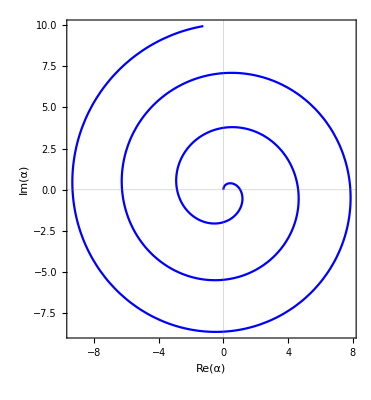

```mathematica
ϵtem=1.16539;
tmin1=tmin[χ,κ,ϵtem,Re[af],Im[af],1,π/2][[1,2]];
Print["minimal time:",tmin1]
ϕ1=Re[phisol[χ,κ,ϵtem,Re[af],Im[af],1][[1,2]]];
Print["phi:",ϕ1]
ParametricPlot[{{Re[Soltime[t,χ,κ,ϵtem,1,ϕ1][[1,1,2]]],Im[Soltime[t,χ,κ,ϵtem,1,ϕ1][[1,1,2]]]}(*,{Re[Soltime[t,χ,κ,ϵtem,-1,ϕ2][[1,1,2]]],Im[Soltime[t,χ,κ,ϵtem,-1,ϕ2][[1,1,2]]]}*)(*{Re[Soltimeminus[t,χ,κ,ϵtem,ϕ1][[1,1,2]]],Im[Soltimeminus[t,χ,κ,ϵtem,ϕ1][[1,1,2]]]}*)},{t,0,tmin1},PlotStyle->{Red,Blue},PlotTheme->"Scientific",FrameStyle->Directive[Thickness[0.003],Black,20],FrameLabel->{"Re(α)","Im(α)"},LabelStyle->Directive[Black,16,FontFamily->"Times"]]
```

```mathematica
(*tmin1=tmin[χ,κ,ϵtem,n,0,1,π/2][[1,2]];
Print["minimal time:",tmin1]
ϕ1=Re[phisol[χ,κ,ϵtem,n,0,1][[1,2]]];
Print["phi:",ϕ1]*)
t1[t_]=Soltime[t,χ,κ,ϵtem,1,ϕ1][[1,1,2]];
```

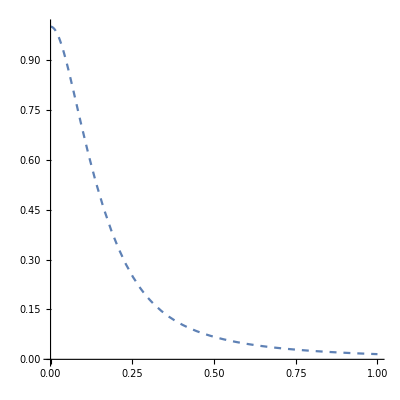

```mathematica
tbar[t_]=I*(ϵtem Sin[χ*t+ϕ1]+I*ϵtem*Cos[χ*t+ϕ1])/(χ-I κ/2);
mean2[t_]=-2Im[D[t1[t],t]*Conjugate[t1[t]]];
var2[t_]=Abs[D[t1[t],t]];
tfig1=ParametricPlot[{Abs[t1[t]]/Abs[t1[tmin1]],ArcCos[Exp[-Abs[t1[t]]^2/2]]/NIntegrate[var2[tt],{tt,0,t}]},{t,10^-4,tmin1},PlotRange->{{0,1},{0,1}},PlotStyle->Dashed]
```

```mathematica
mt1[t_]:=Sin[ArcCos[Exp[-Abs[t1[t]]^2/2]]]^2/(Sqrt[2]*NIntegrate[var2[tt],{tt,0,t}])
ml1[t_]:=Sin[ArcCos[Exp[-Abs[t1[t]]^2/2]]]^2/(2*NIntegrate[var2[tt],{tt,0,t}])
geo1[t_]:=ArcCos[Exp[-Abs[t1[t]]^2/2]]/NIntegrate[var2[tt],{tt,0,t}]
```

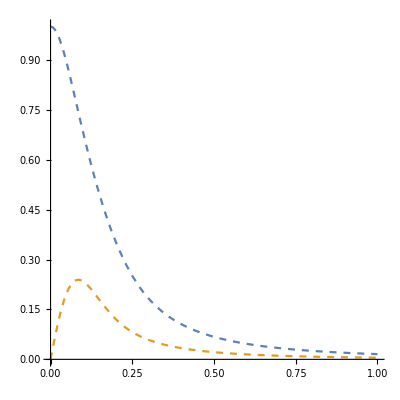

```mathematica
tfig1=ParametricPlot[{{Abs[t1[t]]/Abs[t1[tmin1]],geo1[t]}(*,{Abs[t1[t]]/Abs[t1[tmin1]],mt1[t]}*),{Abs[t1[t]]/Abs[t1[tmin1]],ml1[t]}},{t,10^-4,tmin1},PlotRange->{{0,1},{0,1}},PlotStyle->Dashed]
```

```mathematica
etat=Table[{Abs[t1[t*10/100]]/10,geo1[t*10/100],mt1[t*10/100],ml1[t*10/100]},{t,1,100}];
Export["C:\\Users\\Mo Zhou\\python file\\paint\\新建文件夹\\etat.csv",etat];
```

```mathematica
dotalpha=Table[{Abs[ds[t*10/100]],Abs[var2[t*10/100]],Abs[cd2[t*10/100]]},{t,1,100}];
Export["C:\\Users\\Mo Zhou\\python file\\paint\\新建文件夹\\dotalpha.csv",dotalpha];
```

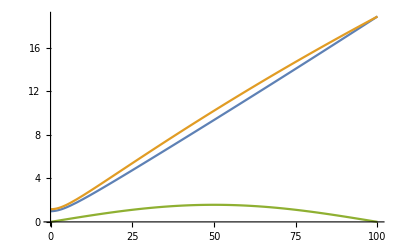

```mathematica
Plot[{Abs[ds[t*10/100]],Abs[var2[t*10/100]],Abs[cd2[t*10/100]]},{t,0,100}]
```

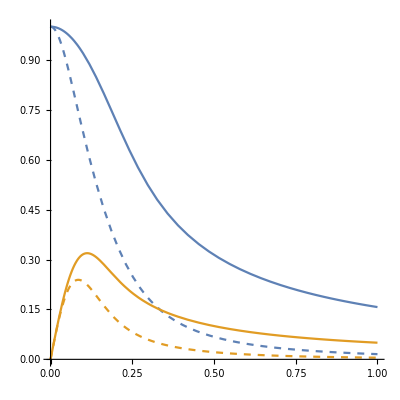

```mathematica
Show[tfig1,figcd]
```

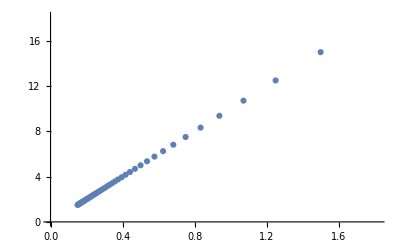

```mathematica
ListPlot[Table[{1.5/(n/50*10),15/(n/50*10)},{n,1,50}]]
```

```mathematica
D[ArcCos[x[t]],t]
```

-x'[t]/(√(1-x[t]^2))